The governing ODE we get for steady-state motion of a frictional landslide governed by a logarithmic friction law:  is

where  is the average slope of the landslide body. The sliding velocity is given by 
 
Let  and we define the landslide thickness . 
We assume an erosion rate  defined on the interval , given us an ODE of the form. For Mathematica to solve it we need to rearrange it to a standard form, but this is the main problem we need to solve.

```mathematica
eqnODE = Tan[θ]*(1+b''[x]/2*H[x])/(1+b'[x]*Tan[θ]) - (b'[x]+f) - H'[x]+ A*Log[H[x]] == A*Log[η (x^2/2+x)]
```

-f+A Log[H[x]]-b'[x]-H'[x]+(Tan[θ] (1+1/2 H[x] b''[x]))/(1+Tan[θ] b'[x])==A Log[(x+x^2/2) η]

-1-0.2 (π Cos[π x]+1.5708 Cos[2 π x]+1.25664 Cos[4 π x]+1.25664 Cos[8 π x]+0.502655 Cos[16 π x])+0.05 Log[H[x]]+(√(5-2 √5) (1+0.1 H[x] (-π^2 Sin[π x]-9.8696 Sin[2 π x]-15.7914 Sin[4 π x]-31.5827 Sin[8 π x]-25.2662 Sin[16 π x])))/(1+0.145309 (π Cos[π x]+1.5708 Cos[2 π x]+1.25664 Cos[4 π x]+1.25664 Cos[8 π x]+0.502655 Cos[16 π x]))-H'[x]==0.05 Log[-0.5 (x+x^2/2)]

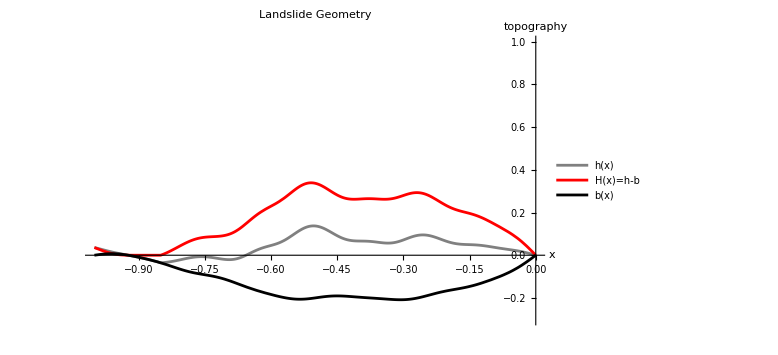

```mathematica
(*Basal topography*)
bmax = 0.2;
bv = bmax*(Sin[ π x] + 0.25*Sin[2π x]+0.1*Sin[4π x]+0.05*Sin[8π x] +0.01*Sin[16π x]);(*add 1-5% perturbation to topography at shorter wavelengths*)
θv = π/5;
fv= 1;
Av = 0.05;
ηv = -0.5;(*Effective erosion rate: this should be negative*)
eqn =Tan[θv]*(1+D[bv,x,x]/2*H[x])/(1+D[bv,x]*Tan[θv]) - (D[bv,x]+fv) - D[H[x],x] + Av*Log[H[x]] == Av*Log[ηv (x^2/2+x)]
(*We will assume that erosion varies linearly over the domain from 0 (at x=-1)-> max (at x = 0)*)
xmin = -10^-6;
solss = NDSolve[{eqn,H[xmin]==10^-6},H,{x,-1,xmin}];
h = bv+ H[x]/. solss;
p1=Plot[{h,H[x]/. solss,bv},{x,-1,xmin},PlotStyle->{{Gray,Thick},{Red},{Black,Thick}},PlotLabel->"Landslide Geometry",AxesLabel->{"x","topography"},PlotLegends->{"h(x)","H(x)=h-b","b(x)"},ImageSize->Large,PlotRange->{-1.5*bmax,5*bmax}]
```

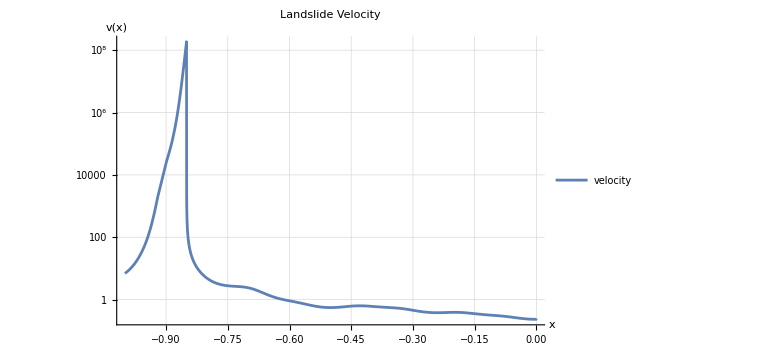

```mathematica
vx = Exp[Tan[θv]*(1+D[bv,x,x]/2*H[x]/.solss)/Av/(1+D[bv,x]*Tan[θv])-(D[h,x]+fv)/Av];
p2=LogPlot[vx,{x,-1,10*xmin},PlotRange->Full,PlotLabel->"Landslide Velocity",AxesLabel->{"x","v(x)"},PlotLegends->{"velocity"},ImageSize->Large,GridLines->Automatic]
```

```mathematica
(*Export["~/Documents/GitHub/landslides/analyticsol/landslide_topography.png",p1]
Export["~/Documents/GitHub/landslides/analyticsol/landslide_vel.png",p2]*)
```

```mathematica
(*(*Parameters*)
n=512;             (*number of points*)
L=1.0;             (*domain length*)
H=0.7;             (*Hurst exponent—controls roughness*)
seed=123;

(*Generate fractional Brownian motion*)
SeedRandom[seed];
fbm=Accumulate@RandomVariate[NormalDistribution[0,(L/n)^H],n];

(*Rescale domain*)
xvals=Subdivide[-L,0,n-1];
roughLine=Interpolation[Transpose[{xvals,fbm}],InterpolationOrder->1];

(*Plot it*)
Plot[roughLine[x],{x,-L,0},PlotLabel->"Self-Affine Rough Line",AxesLabel->{"x","f(x)"}]*)
```